#### Functions

```mathematica
Clear[ρ]
Δ[θ_,θ0_,α_?NumericQ]:=α Log[θ/θ0]-θ+θ0
θ0[θ_?NumericQ,δ_?NumericQ,α_?NumericQ]:=θ0/.FindRoot[Δ[θ,θ0,α]==δ,{θ0,α+θ}]//Re
(*ρ[θ_,θ0_?NumericQ,α_?NumericQ]:=(√((θ0-α)^2+θ0^2)θ0/(θ0-α)(θ-α)^2/(2 θ^2-2α θ+α^2))*1/(√(2π))Exp[-θ0^2/2]HeavisideTheta[θ0-α]*)
ρ[θ_,θ0_?NumericQ,α_?NumericQ]:=(θ0(√(θ0^2+(θ0-α)^2))/(θ^2+(θ-α)^2)(√((θ-α)^2))/(θ0-α))*1/(√(2π))Exp[-θ0^2/2]HeavisideTheta[θ0-α]
```

```mathematica
aa={0.1,0.5,1.0};inds=Table[i,{i,1,Length[aa]}];
```

#### 2D density

```mathematica
ContourPlot[ρ[θ,θ0[θ,δ,1.0],1.0],
{δ,0,0.5},{θ,0,2},
PlotRange->All,
FrameLabel->{Style["Δ",Bold,FontSize->16],Style["θ",Bold,FontSize->16]},
FrameTicksStyle->14,ImageSize->Medium];
```

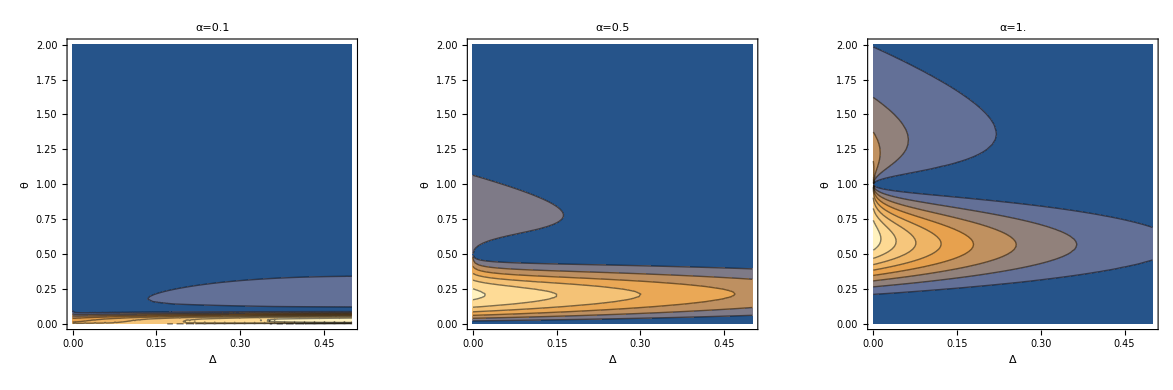

```mathematica
ctplt=ContourPlot[ρ[θ,θ0[θ,δ,#],#],
{δ,0,0.5},{θ,0,2},
PlotRange->All,
FrameLabel->{Style["Δ",Bold,FontSize->16],Style["θ",Bold,FontSize->16]},
PlotLabel->Style["α="<>ToString[#],FontSize->16],ImageSize->Medium]&/@aa;
GraphicsRow[ctplt]
```

#### Marginalise at selected points

```mathematica
df=3.0;dd=df/30;
deltas=Table[δ,{δ,0.0,df,dd}];
points=Table[NIntegrate[ρ[θ,θ0[θ,δ,aa[[#]]],aa[[#]]],{θ,0,5},MaxRecursion->12],{δ,0.0,df,dd}]&/@inds;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in θ near {θ} = {0.100598}. NIntegrate obtained 0.652727 and 1.10444×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in θ near {θ} = {0.100598}. NIntegrate obtained 0.668238 and 1.43494×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in θ near {θ} = {0.100598}. NIntegrate obtained 0.668081 and 1.68251×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

#### Plot marginalised pdf

```mathematica
lgdata=MapThread[Flatten@*List,{deltas,#}]&/@Log[points];
lines=b+c*x/.FindFit[lgdata[[#]],b+c*x,{{b,0.01},c},x]&/@inds
lgplt=Show[
ListPlot[lgdata],
ListPlot[TemporalData[lines/.(x->deltas),{deltas}],Joined->True],
PlotRange->All,
AxesLabel->{"Δ","Log[p(Δ)]"}
];
```

{0.453438-1.54572 x,0.413973-3.2902 x,-0.409667-5.14157 x}

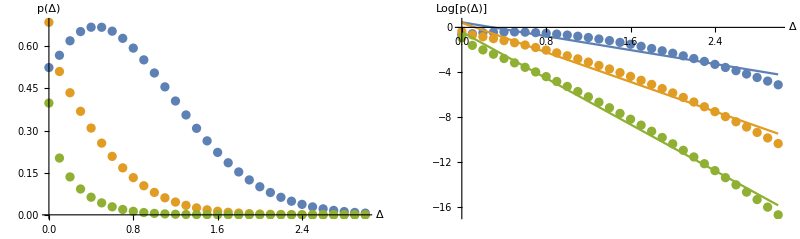

```mathematica
lndata=MapThread[Flatten@*List,{deltas,#}]&/@points;
lnplt=ListPlot[lndata,PlotRange->All,AxesLabel->{"Δ","p(Δ)"}];
GraphicsRow[{lnplt,lgplt},PlotRange->All,ImageSize->Full]
Export[NotebookDirectory[]<>"RayWallPressure/pdf.pdf",%];
```

#### Pressure

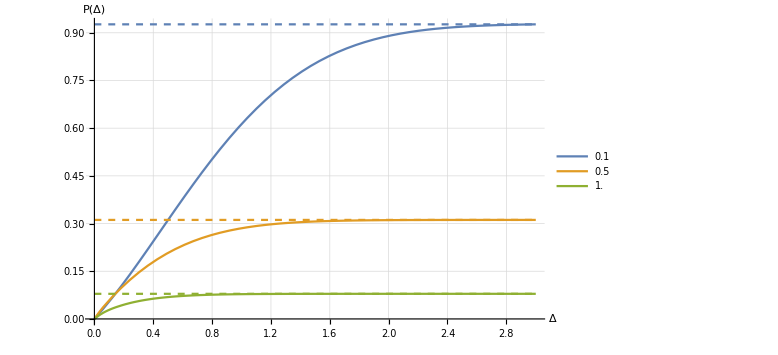

```mathematica
f=Interpolation[lndata[[#]]]&/@inds;
prs=Plot[
NIntegrate[f[[#]][x],{x,0,δ}]&/@inds//Evaluate,
{δ,0,df},
AxesLabel->{"Δ","P(Δ)"},GridLines->Automatic,
PlotLegends->aa];//Quiet
Show[{
prs,
Plot[{NIntegrate[f[[#]][x],{x,0,df}]&/@inds//Evaluate},{x,0,df},PlotStyle->{Dashed}]},
ImageSize->Large
]
Export[NotebookDirectory[]<>"RayWallPressure/pressure.pdf",%];
```

```mathematica
Manipulate[NIntegrate[f[[#]][x],{x,0,δ}]&/@inds*aa,
{{δ,df},0,df}]
```